```mathematica
(* Five-spin order: {A,1,2,3,B}.  S = sigma/2. *)
ClearAll["Global`*"];
Nspin = 5;
dim = 2^Nspin;
J = 1.;
delta = 0.5;
omegaA = 0.6;
omegaB = 0.9;
gList = Range[0., 0.5, 0.001];
```

```mathematica
id = IdentityMatrix[2];
sx0 = PauliMatrix[1]/2;
sy0 = PauliMatrix[2]/2;
sz0 = PauliMatrix[3]/2;
op[a_, j_] := KroneckerProduct @@ ReplacePart[ConstantArray[id, Nspin], j -> a];
sx[j_] := op[sx0, j];
sy[j_] := op[sy0, j];
sz[j_] := op[sz0, j];
sp[j_] := sx[j] + I sy[j]; sm[j_] := sx[j] - I sy[j];
```

```mathematica
Hchain = J (sx[2].sx[3] + sy[2].sy[3] + delta sz[2].sz[3]+sx[3].sx[4] + sy[3].sy[4] + delta sz[3].sz[4]);
```

```mathematica
(* 1. ZZ coupling, no Zeeman splitting *)
ezz0 = Table[Sort[Chop[Eigenvalues[N[Hchain + g Vzz]]]], {g, gList}];
```

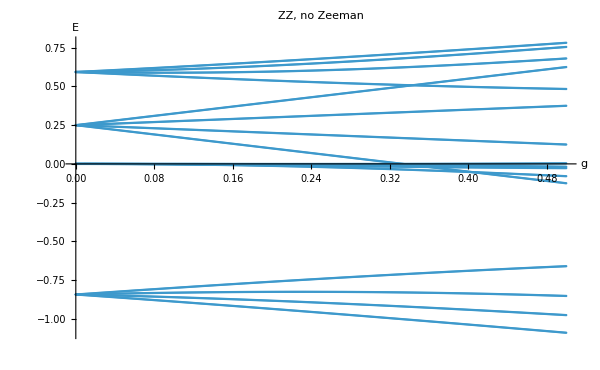

```mathematica
p1 = ListPlot[Flatten[Table[{gList[[i]], ezz0[[i, j]]}, {i, Length[gList]}, {j, dim}], 1],
   PlotRange -> All, AxesLabel -> {"g", "E"}, PlotLabel -> "ZZ, no Zeeman",ImageSize->600]
```

```mathematica
(* 2. ZZ coupling, with probe Zeeman splitting *)
ezzZ = Table[Sort[Chop[Eigenvalues[N[Hchain + HZ + g Vzz]]]], {g, gList}];
```

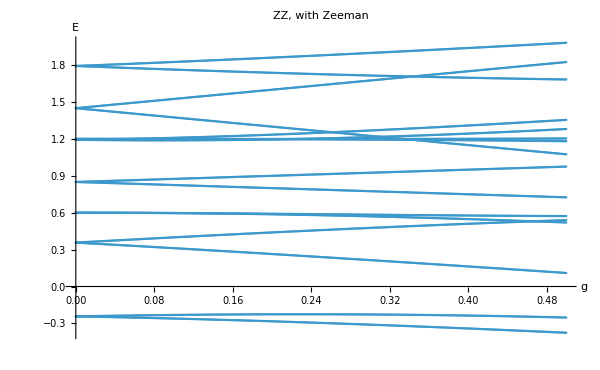

```mathematica
p2 = ListPlot[Flatten[Table[{gList[[i]], ezzZ[[i, j]]}, {i, Length[gList]}, {j, dim}], 1],
   PlotRange -> All, AxesLabel -> {"g", "E"}, PlotLabel -> "ZZ, with Zeeman",ImageSize->600]
```

```mathematica
(* 3. Exchange coupling, no Zeeman splitting *)
eex0 = Table[Sort[Chop[Eigenvalues[N[Hchain + g Vex]]]], {g, gList}];
```

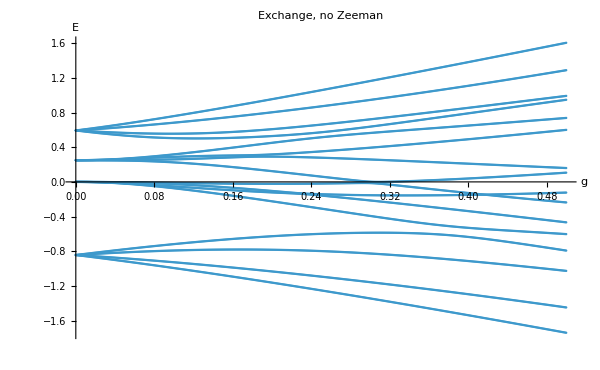

```mathematica
p3 = ListPlot[Flatten[Table[{gList[[i]], eex0[[i, j]]}, {i, Length[gList]}, {j, dim}], 1],
   PlotRange -> All, AxesLabel -> {"g", "E"}, PlotLabel -> "Exchange, no Zeeman",ImageSize->600]
```

```mathematica
(* 4. Exchange coupling, with probe Zeeman splitting *)
eexZ = Table[Sort[Chop[Eigenvalues[N[Hchain + HZ + g Vex]]]], {g, gList}];
```

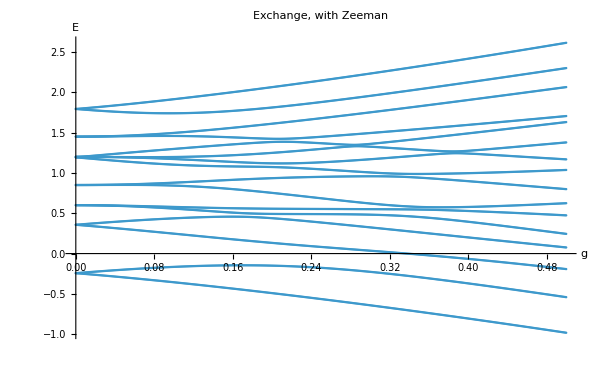

```mathematica
p4 = ListPlot[Flatten[Table[{gList[[i]], eexZ[[i, j]]}, {i, Length[gList]}, {j, dim}], 1],
   PlotRange -> All, AxesLabel -> {"g", "E"}, PlotLabel -> "Exchange, with Zeeman",ImageSize->600]
```

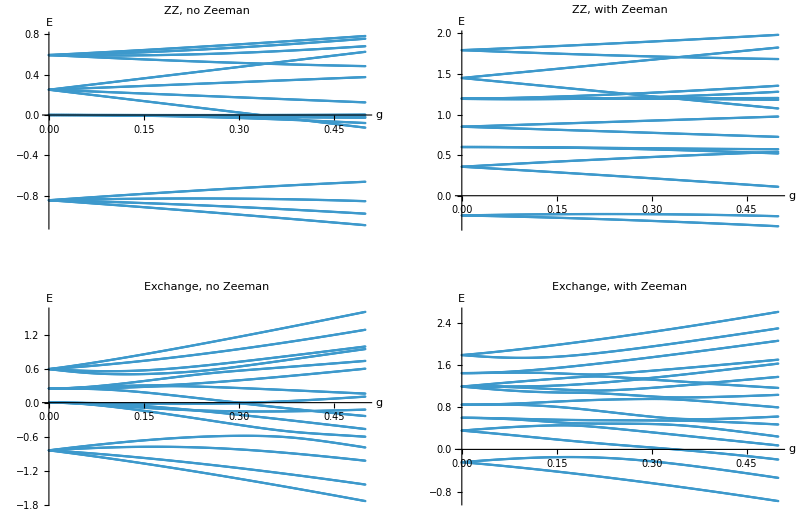

```mathematica
GraphicsGrid[{{p1, p2}, {p3, p4}}, ImageSize -> 800]
```

```mathematica
ClearAll["Global`*"];

L=5;
J=1.;
delta=10.;
gList=Range[0.,1.,0.001];

id=IdentityMatrix[2];
sx0=PauliMatrix[1]/2;
sy0=PauliMatrix[2]/2;
sz0=PauliMatrix[3]/2;

op[a_,j_]:=KroneckerProduct@@ReplacePart[ConstantArray[id,L],j->a];

sx[j_]:=op[sx0,j];
sy[j_]:=op[sy0,j];
sz[j_]:=op[sz0,j];

bond[i_,j_]:=J (sx[i].sx[j]+sy[i].sy[j]+delta sz[i].sz[j]);
Hbulk=bond[2,3]+bond[3,4];
Vedge=bond[1,2]+bond[4,5];
```

```mathematica
energies=Table[Sort[Chop[Eigenvalues[N[Hbulk+g Vedge]]]],{g,gList}];
```

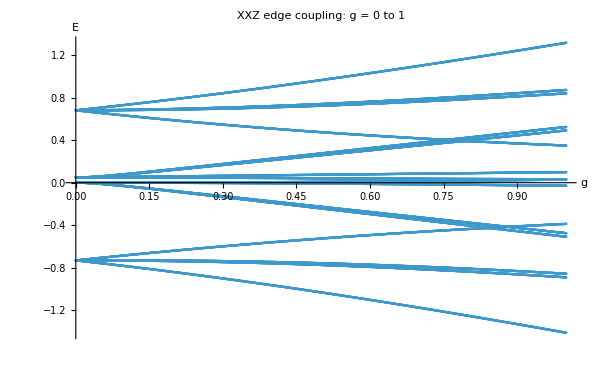

```mathematica
ListPlot[Flatten[Table[{gList[[i]],energies[[i,n]]},{i,Length[gList]},{n,2^L}],1],PlotRange->All,AxesLabel->{"g","E"},PlotLabel->"XXZ edge coupling: g = 0 to 1",ImageSize->600]
```

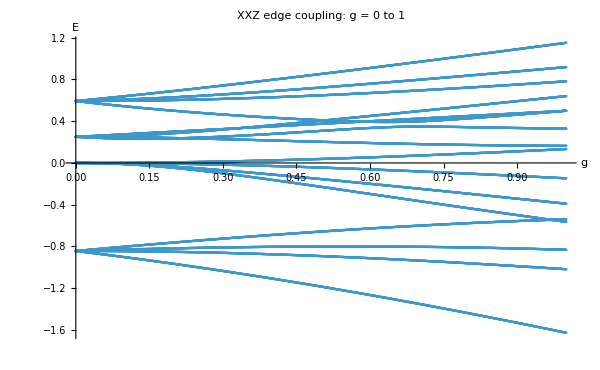

```mathematica
ListPlot[Flatten[Table[{gList[[i]],energies[[i,n]]},{i,Length[gList]},{n,2^L}],1],PlotRange->All,AxesLabel->{"g","E"},PlotLabel->"XXZ edge coupling: g = 0 to 1",ImageSize->600]
```

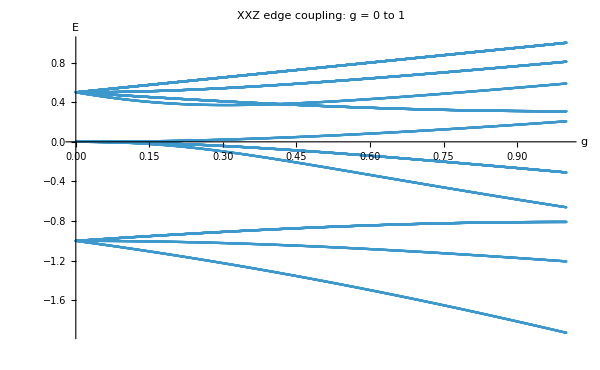

```mathematica
ListPlot[Flatten[Table[{gList[[i]],energies[[i,n]]},{i,Length[gList]},{n,2^L}],1],PlotRange->All,AxesLabel->{"g","E"},PlotLabel->"XXZ edge coupling: g = 0 to 1",ImageSize->600]
```

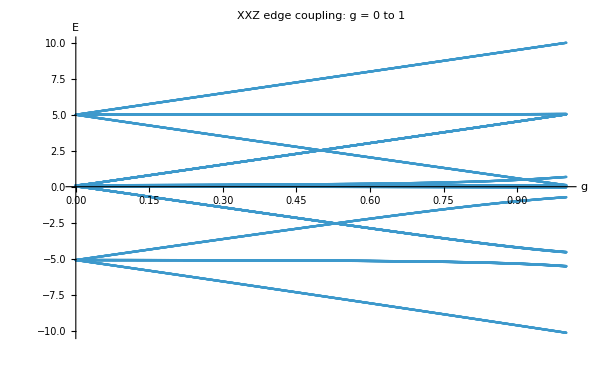

```mathematica
ListPlot[Flatten[Table[{gList[[i]],energies[[i,n]]},{i,Length[gList]},{n,2^L}],1],PlotRange->All,AxesLabel->{"g","E"},PlotLabel->"XXZ edge coupling: g = 0 to 1",ImageSize->600]
```